# GeoCommunityGraphPlot

Create a graph on a map with communities highlighted with different colors

## Definition

```mathematica
ClearAll[GeoCommunityGraphPlot]
$default13$1Pallet=Catenate[];
purpleHue=5/6;
plotStyleParser[Automatic,"Rainbow",communityCount_Integer]:=
Table[Hue[purpleHue (i/(communityCount-1))],{i,0,communityCount-1}]
plotStyleParser[Automatic,"Default_13.1",_]=$default13$1Pallet;
plotStyleParser[l:{__?ColorQ},_,_]:=l

GeoCommunityGraphPlot::clrmsmtch="Warning: there are less colors, `1` in \"CommunityColors\" than communities, `2`";
GeoCommunityGraphPlot[expr_]:=
With[{communities=FindGraphCommunities@expr},
If[
ListQ@OptionValue["CommunityColors"]&&
Length[OptionValue["CommunityColors"]]<Length[communities],
Message[GeoCommunityGraphPlot::clrmsmtch,Length[OptionValue["CommunityColors"]],Length[communities]]];
GeoGraphPlot[
Catenate@MapThread[
Table[Style[location,#2],{location,#1}]&,
{communities,
PadRight[{},Length[communities],
plotStyleParser[OptionValue["CommunityColors"],Length[communities]]]}],
EdgeList@expr]]
```

## Documentation

### Usage

GeoCommunityGraphPlot[graph]

generates a geographic plot showing the community structure of the graph graph.

### Details & Options

This function code was created by Eric Parfitt.

## Examples

### Basic Examples

Nest the operation of finding bordering countries for a country to create a graph of bordering countries in Europe, Africa, and Asia:

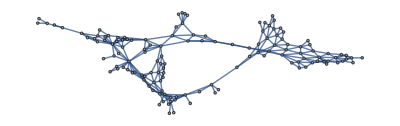

```mathematica
graph=UndirectedGraph@NestGraph[CountryData[#,"BorderingCountries"]&,Entity["Country","France"],12]
```

Plot the graph on a map:

```mathematica
GeoCommunityGraphPlot[graph]
```

-Graphics-

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery and Eric Parfitt

### Keywords

Geography

Graph

Networks

Graph communities

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related Symbols

CommunityGraphPlot

GeoGraphics

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.